# Polynomial approximation of χ^2 percent point function

This function is an inverse for CDF

```mathematica
ChiSquarePPF[dof_,p_]:=x /. NSolve[Rationalize[CDF[ChiSquareDistribution[dof],x]==0.95],x][[1]];
```

So it’s not easy to calculate the value of this function in C code. We need to calculate PPF with given significance level p for different dof (degrees of freedom).

We consider p=0.95. Plot for this case is presented below.

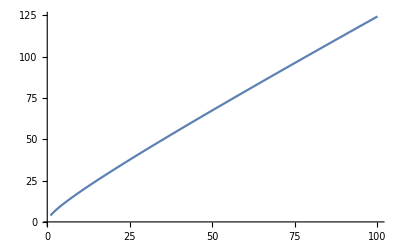

```mathematica
Plot[ChiSquarePPF[dof,0.95],{dof,1,100}]
```

This function for dof > 20 looks close to linear. We can divide function domain in two parts (0,20) and [20,∞), and use different approximations for these intervals.

## DOF > 20

9.27863+1.157 x

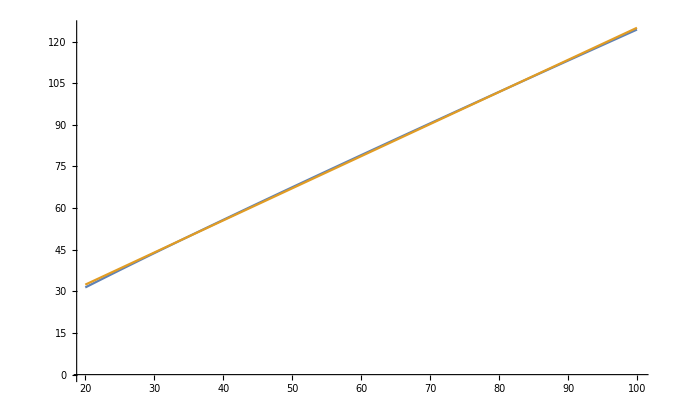

```mathematica
data = Table[{dof,ChiSquarePPF[dof,0.95]},{dof,20, 100}];
f=Fit[data, {1, x},x]
fdata=Table[{x,f}, {x,20, 100}];
ListLinePlot[{data, fdata}]
```

## DOF < 20

2.10308+1.98911 x-0.0464057 x^2+0.00102171 x^3

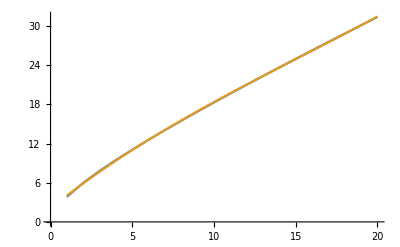

```mathematica
data = Table[{dof,ChiSquarePPF[dof,0.95]},{dof,1, 20}];
f=Fit[data, {1, x, x^2,x^3},x]
fdata=Table[{x,f}, {x,1, 20}];
ListLinePlot[{data, fdata}]
```